Data options

```mathematica
EarlyOrLate="Late";(*Early,Late,or All*)
BeamNoBeam = "NoBeam";
subtract1point5=True;
```

```mathematica
Dst=-25;
dstStr=ToString[Dst];
```

```mathematica
GoverK=2;
GoverKStr=ToString[GoverK];
```

Setup input files

```mathematica
inDir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/txtOutput/";
```

```mathematica
earlyNames={"20180511-20_50-22_25MLT-Dst"<>dstStr<>"-ionBeam-data-allALT-BOTH-GKDec"<>GoverKStr<>"-Kchi2Max5_0-combo.csv",
"20180511-20_50-22_25MLT-Dst"<>dstStr<>"-noBeam-data-allALT-BOTH-GKDec"<>GoverKStr<>"-Kchi2Max5_0-combo.csv"};
```

```mathematica
lateNames={"20180511-22_25-1_50MLT-Dst"<>dstStr<>"-ionBeam-data-allALT-BOTH-GKDec"<>GoverKStr<>"-Kchi2Max5_0-combo.csv",
"20180511-22_25-1_50MLT-Dst"<>dstStr<>"-noBeam-data-allALT-BOTH-GKDec"<>GoverKStr<>"-Kchi2Max5_0-combo.csv"};
```

```mathematica
allNames={"20180511-20_50-1_50MLT-Dst"<>dstStr<>"-ionBeam-data-allALT-NORTH-GKDec"<>GoverKStr<>"-Kchi2Max5_0-combo.csv",
"20180511-20_50-1_50MLT-Dst"<>dstStr<>"-noBeam-data-allALT-NORTH-GKDec"<>GoverKStr<>"-Kchi2Max5_0-combo.csv"};
```

### Read in array of kappa values

```mathematica
Switch[ToUpperCase[EarlyOrLate],
"EARLY",
names=earlyNames;,
"LATE",
names=lateNames;,
"ALL",
names=allNames;
]
```

```mathematica
Switch[BeamNoBeam//ToUpperCase,
"BEAM",
fName=names[[1]];,
"NOBEAM",
fName=names[[2]];
]
```

```mathematica
data=Import[inDir<>fName]//Flatten;
```

```mathematica
If[subtract1point5,subVal=1.5,subVal=0];
```

```mathematica
data=data-subVal;
plotMin=1.5-subVal;
plotMax=20;
```

Now check ‘er out

```mathematica
this=SmoothKernelDistribution[data]
```

DataDistribution[…]

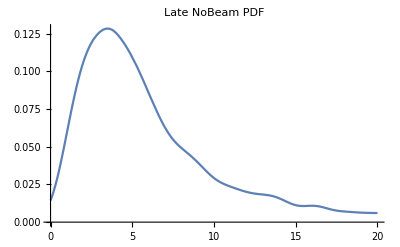
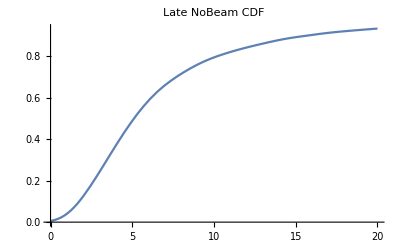

```mathematica
Table[Plot[f[this,x],{x,plotMin,plotMax},PlotLabel->(EarlyOrLate<>" "<>BeamNoBeam<>" "<>ToString[f])],{f,{PDF,CDF}}]
```

```mathematica
candidateDists=FindDistribution[data,3,PerformanceGoal->"Quality"]
```

{FrechetDistribution[2.19349,6.37421,-2.70978],ParetoDistribution[7.,1.51333,0.630561,-0.0801092],MixtureDistribution[{0.787111,0.212889},{LogisticDistribution[4.3179,1.26582],LogNormalDistribution[2.83458,0.535528]}]}

```mathematica
IGParms=FindDistributionParameters[data,InverseGaussianDistribution[μ,λ]]
```

{μ→5.41127,λ→4.98111}

```mathematica
strippedCandidates={InverseGaussianDistribution[μ,λ]/.IGParms};
```

```mathematica
(*strippedCandidates=((candidateDists[[#]])[[2]])[[1]]&/@{1,2,3};*)
```

```mathematica
strippedCandidates=(If[ToString[Head[candidateDists[[#]]]]=="MixtureDistribution",((candidateDists[[#]])[[2]])[[1]],candidateDists[[#]]])&/@Range[Length@candidateDists]
```

{FrechetDistribution[2.19349,6.37421,-2.70978],ParetoDistribution[7.,1.51333,0.630561,-0.0801092],LogisticDistribution[4.3179,1.26582]}

```mathematica
(*Table[Histogram[data,bins,"PDF",PlotLabel->(EarlyOrLate<>" "<>BeamNoBeam<>" "<>ToString[bins])],{bins,{{0.75},"Sturges","Scott","FreedmanDiaconis","Knuth","Wand"}}]*)
```

#### A new go

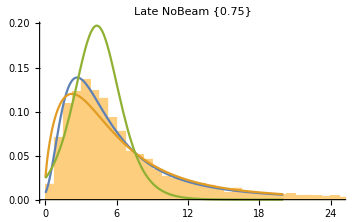
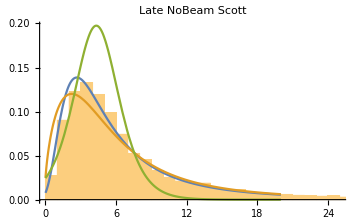
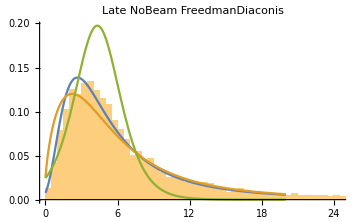
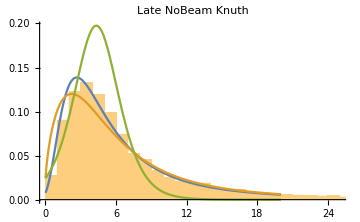
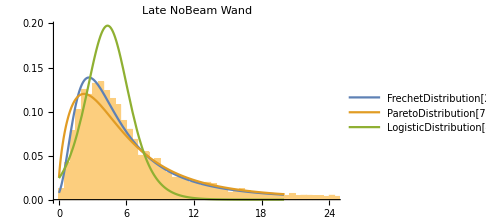

```mathematica
Table[plotLegends=If[ToString[bins]=="Wand",(ToString[#]& /@ strippedCandidates),None];
Show[
Histogram[data,bins,"PDF",PlotLabel->(EarlyOrLate<>" "<>BeamNoBeam<>" "<>ToString[bins]),ImageSize->Medium],Plot[Evaluate[PDF[#,x]&/@ strippedCandidates],{x,plotMin,plotMax},PlotLegends->plotLegends]],{bins,{{0.75},"Scott","FreedmanDiaconis","Knuth","Wand"}}]
```

```mathematica
Table[CDF[dist,1.5-subVal]*100,{dist,strippedCandidates}]
```

{0.146005,0.126069,3.19489}

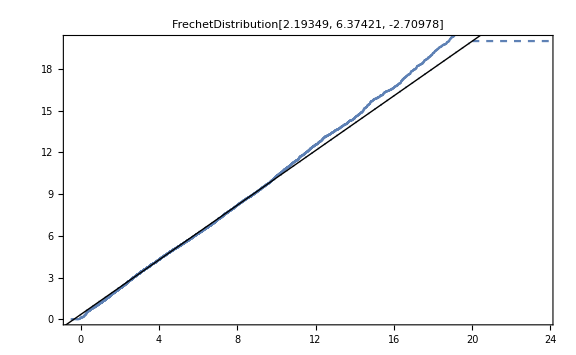
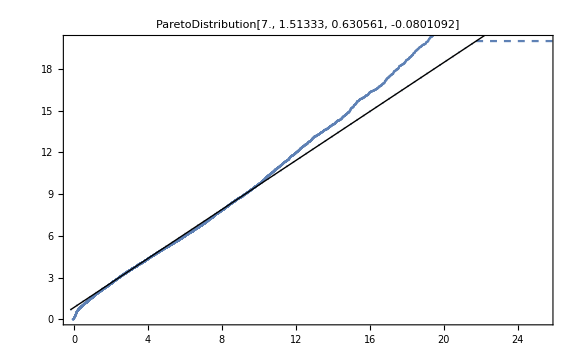
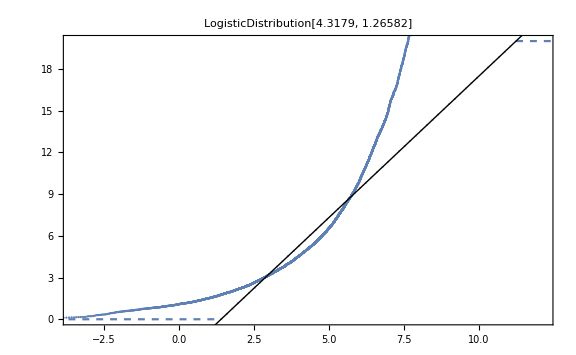

```mathematica
Table[QuantilePlot[data,dist,PlotLabel->ToString[dist],PlotRange->{plotMin,plotMax},ImageSize->Large],{dist,strippedCandidates}]
```

```mathematica
Table[Through[{Mean,Median,(FindMaximum[{PDF[#,x],(1.5-subVal)≤x<101},{x,(1.5-subVal)}]&)}[dist]],{dist,strippedCandidates}]
```

Power::infy: Infinite expression 1/0. encountered.

{{7.69843,4.82365,{0.138651,{x→2.66124}}},{7.59093,4.8901,{0.120073,{x→2.22964}}},{4.3179,4.3179,{0.1975,{x→4.3179}}}}

#### Late NoBeam

```mathematica
Table[plotLegends=If[ToString[bins]=="Wand",(ToString[#]& /@ strippedCandidates),None];
Show[
Histogram[data,bins,"PDF",PlotLabel->(EarlyOrLate<>" "<>BeamNoBeam<>" "<>ToString[bins]),ImageSize->Medium],Plot[Evaluate[PDF[#,x]&/@ strippedCandidates],{x,plotMin,plotMax},PlotLegends->plotLegends]],{bins,{{0.75},"Scott","FreedmanDiaconis","Knuth","Wand"}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[CDF[dist,1.5-subVal]*100,{dist,strippedCandidates}]
```

{0.146005,0.126069,3.19489}

```mathematica
Table[QuantilePlot[data,dist,PlotLabel->ToString[dist],PlotRange->{plotMin,plotMax},ImageSize->Large],{dist,strippedCandidates}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Through[{Mean,Median,(FindMaximum[{PDF[#,x],(1.5-subVal)≤x<101},{x,(1.5-subVal)}]&)}[dist]],{dist,strippedCandidates}]
```

Power::infy: Infinite expression 1/0. encountered.

{{7.69843,4.82365,{0.138651,{x→2.66124}}},{7.59093,4.8901,{0.120073,{x→2.22964}}},{4.3179,4.3179,{0.1975,{x→4.3179}}}}

#### Early NoBeam

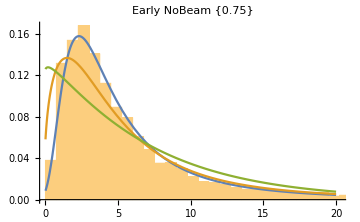
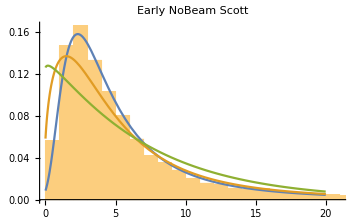
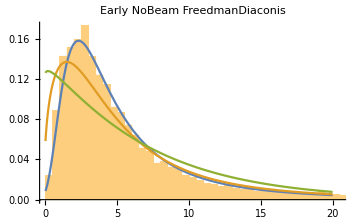
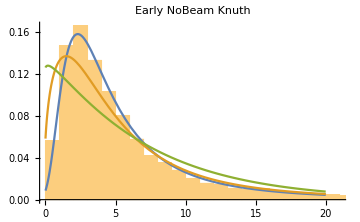
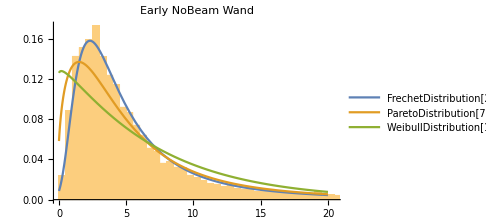

```mathematica
Table[plotLegends=If[ToString[bins]=="Wand",(ToString[#]& /@ strippedCandidates),None];
Show[
Histogram[data,bins,"PDF",PlotLabel->(EarlyOrLate<>" "<>BeamNoBeam<>" "<>ToString[bins]),ImageSize->Medium],Plot[Evaluate[PDF[#,x]&/@ strippedCandidates],{x,plotMin,plotMax},PlotLegends->plotLegends]],{bins,{{0.75},"Scott","FreedmanDiaconis","Knuth","Wand"}}]
```

```mathematica
Table[CDF[dist,1.5-subVal]*100,{dist,strippedCandidates}]
```

{0.139033,0.404885,1.22347}

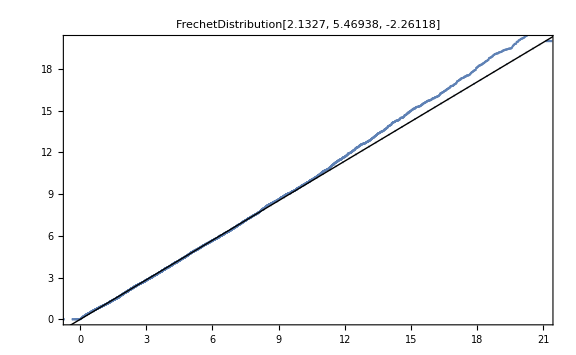
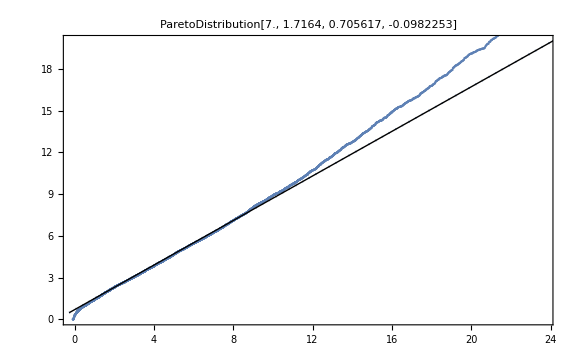
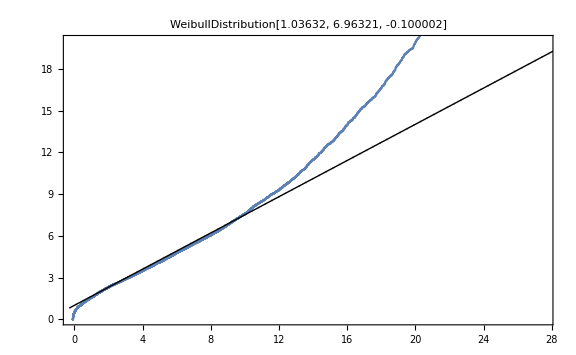

```mathematica
Table[QuantilePlot[data,dist,PlotLabel->ToString[dist],PlotRange->{plotMin,plotMax},ImageSize->Large],{dist,strippedCandidates}]
```

```mathematica
Table[Through[{Mean,Median,(FindMaximum[{PDF[#,x],(1.5-subVal)≤x<101},{x,(1.5-subVal)}]&)}[dist]],{dist,strippedCandidates}]
```

Power::infy: Infinite expression 1/0. encountered.

{{6.87966,4.23373,{0.157888,{x→2.3059}}},{6.84273,4.17925,{0.136833,{x→1.48401}}},{6.76352,4.78893,{0.127778,{x→0.174478}}}}

#### LateBeam

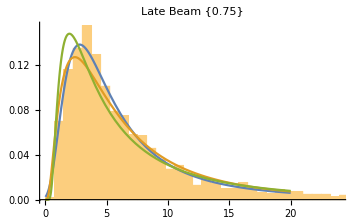
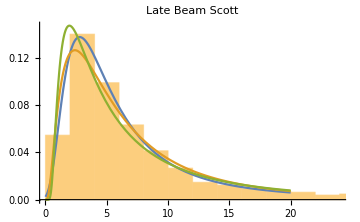
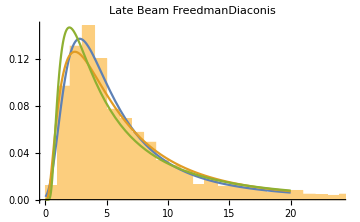
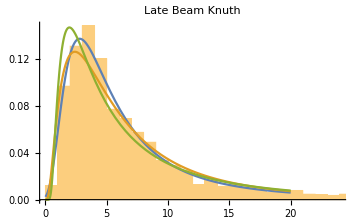
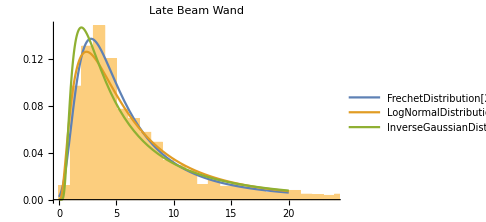

```mathematica
Table[plotLegends=If[ToString[bins]=="Wand",(ToString[#]& /@ strippedCandidates),None];
Show[
Histogram[data,bins,"PDF",PlotLabel->(EarlyOrLate<>" "<>BeamNoBeam<>" "<>ToString[bins]),ImageSize->Medium],Plot[Evaluate[PDF[#,x]&/@ strippedCandidates],{x,plotMin,plotMax},PlotLegends->plotLegends]],{bins,{{0.75},"Scott","FreedmanDiaconis","Knuth","Wand"}}]
```

```mathematica
Table[CDF[dist,1.5-subVal]*100,{dist,strippedCandidates}]
```

{0.0321079,0,0}

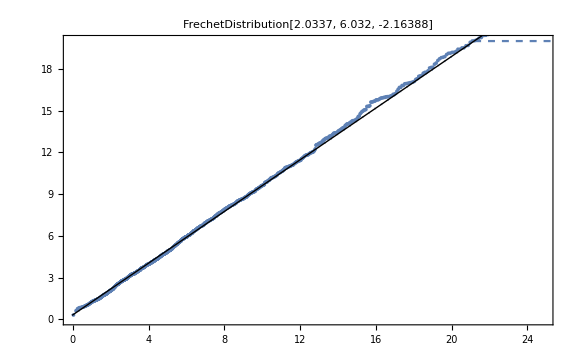
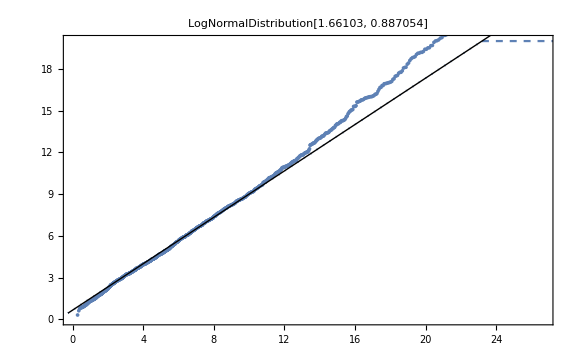
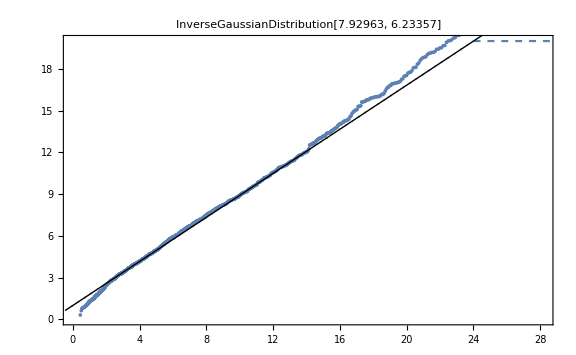

```mathematica
Table[QuantilePlot[data,dist,PlotLabel->ToString[dist],PlotRange->{plotMin,plotMax},ImageSize->Large],{dist,strippedCandidates}]
```

```mathematica
Table[Through[{Mean,Median,(FindMaximum[{PDF[#,x],(1.5-subVal)≤x<101},{x,(1.5-subVal)}]&)}[dist]],{dist,strippedCandidates}]
```

{{8.3568,5.05933,{0.137744,{x→2.79127}}},{7.80264,5.26473,{0.126605,{x→2.39688}}},{7.92963,4.93479,{0.1474,{x→1.95195}}}}

#### Early beam

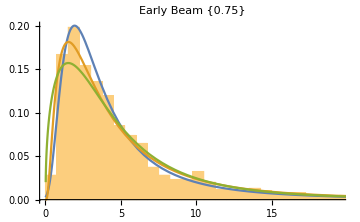
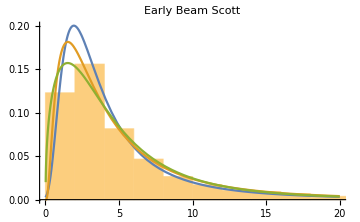
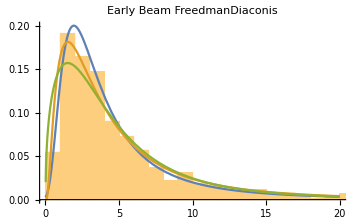
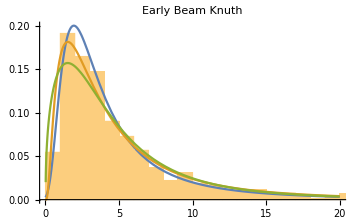
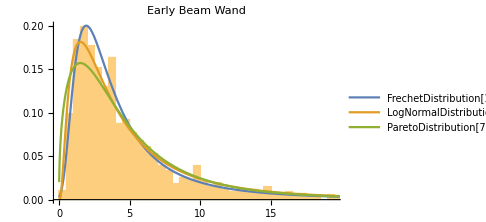

```mathematica
Table[plotLegends=If[ToString[bins]=="Wand",(ToString[#]& /@ strippedCandidates),None];
Show[
Histogram[data,bins,"PDF",PlotLabel->(EarlyOrLate<>" "<>BeamNoBeam<>" "<>ToString[bins]),ImageSize->Medium],Plot[Evaluate[PDF[#,x]&/@ strippedCandidates],{x,plotMin,plotMax},PlotLegends->plotLegends]],{bins,{{0.75},"Scott","FreedmanDiaconis","Knuth","Wand"}}]
```

```mathematica
Table[CDF[dist,1.5-subVal]*100,{dist,strippedCandidates}]
```

{0,0,0.000705345}

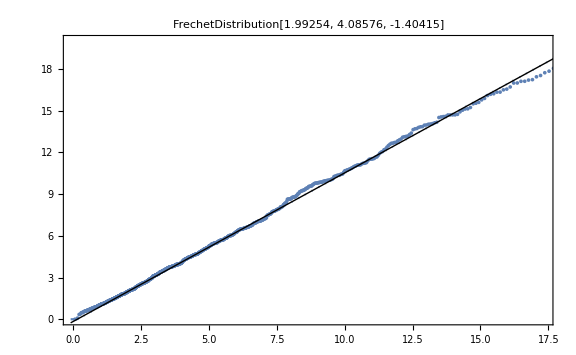
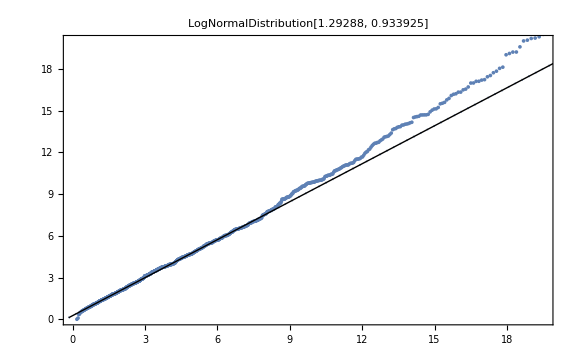
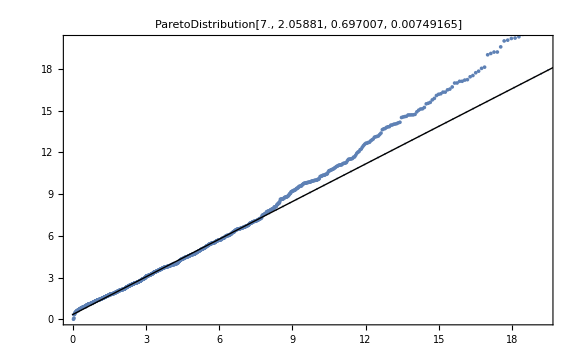

```mathematica
Table[QuantilePlot[data,dist,PlotLabel->ToString[dist],PlotRange->{plotMin,plotMax},ImageSize->Large],{dist,strippedCandidates}]
```

```mathematica
Table[QuantilePlot[data,dist,PlotLabel->ToString[dist],PlotRange->All,ImageSize->Medium],{dist,strippedCandidates}]
```

```mathematica
Table[Through[{Mean,Median,(FindMaximum[{PDF[#,x],(1.5-subVal)≤x<101},{x,(1.5-subVal)}]&)}[dist]],{dist,strippedCandidates}]
```

Power::infy: Infinite expression 1/0. encountered.

{{5.86439,3.50671,{0.20006,{x→1.92725}}},{5.63493,3.64326,{0.181346,{x→1.52297}}},{5.51992,3.7053,{0.157107,{x→1.50992}}}}

```mathematica
EBParms={{5.864388537347294,3.5067147684690703,{0.2000600583260706,{x->1.927245673666103}}},{5.634933494839454,3.6432556152439752,{0.18134589016548325,{x->1.5229706234327138}}},{5.519916657273108,3.705297479597681,{0.15710707424494613,{x->1.5099237854305736}}}};
```

```mathematica
Flatten@Values@EBParms[[;;,3,2]]+1.5
```

{3.42725,3.02297,3.00992}

```mathematica
LBParms={{8.356799803932669,5.0593260799963415,{0.13774372258611142,{x->2.7912731887820987}}},{7.802640215940831,5.264731549219105,{0.1266045581780007,{x->2.396877118512621}}},{7.929627341188286,4.934794306686537,{0.1474001318942657,{x->1.9519499524175183}}}};
```

```mathematica
Flatten@Values@LBParms[[;;,3,2]]+1.5
```

{4.29127,3.89688,3.45195}

```mathematica
ENParms={{6.879662260334056,4.23373383820487,{0.15788790332793753,{x->2.3058982806190587}}},{6.842731598298872,4.179252811014436,{0.13683316760409212,{x->1.4840134262664053}}},{6.763522611152089,4.78892784660737,{0.12777793057338993,{x->0.1744775190151619}}}};
```

```mathematica
Flatten@Values@ENParms[[;;,3,2]]+1.5
```

{3.8059,2.98401,1.67448}

```mathematica
LNParms={{7.698433271657989,4.823652375098122,{0.13865100317320003,{x->2.661235745481003}}},{7.590932678095778,4.890095364561198,{0.12007305636156058,{x->2.2296379317178756}}},{4.31790441858939,4.31790441858939,{0.19750016926399971,{x->4.317904744963767}}}};
```

```mathematica
Flatten@Values@LNParms[[;;,3,2]]+1.5
```

{4.16124,3.72964,5.8179}